Single Variable Calculus part of assignment

Exercise 1

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
Integrate[x^n, x]
```

x^(1+n)/(1+n)

```mathematica
D[Sin[x], x]
```

Cos[x]

```mathematica
Integrate[Sin[x], x]
```

-Cos[x]

```mathematica
D[Cos[x], x]
```

-Sin[x]

```mathematica
Integrate[Sin[x], x]
```

-Cos[x]

```mathematica
D[Exp[x], x]
```

ⅇ^x

```mathematica
Integrate[Exp[x],x]
```

ⅇ^x

```mathematica
D[Log[x], x]
```

1/x

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]

```mathematica
D[b^x, x]
```

b^x Log[b]

```mathematica
Integrate[b^x, x]
```

b^x/Log[b]

Exercise 2

```mathematica
D[(4x^2)+(3x^2)-5x+4, x]
```

-5+14 x

Exercise 3

```mathematica
D[((x^3)-1)^100, x]
```

300 x^2 (-1+x^3)^99

Exercise 4

```mathematica
Integrate[Sqrt[2x+1], {x, 0, 4}]
```

26/3

Exercise 5

```mathematica
D[Sqrt[x]*(1-x), x]
```

(1-x)/(2 √x)-√x

Exercise 6

```mathematica
Integrate[x*Exp[-x], {x, 1, 2}]
```

(-3+2 ⅇ)/ⅇ^2

Exercise 7

```mathematica
D[A*Exp[k*t], t]
```

A ⅇ^(k t) k

```mathematica
Integrate[A*Exp[k*t], t]
```

(A ⅇ^(k t))/k

```mathematica
D[m*x+b, x]
```

m

```mathematica
Integrate[m*x+b, x]
```

b x+(m x^2)/2

```mathematica
D[a*(x^n)+b, x]
```

a n x^(-1+n)

```mathematica
Integrate[a*(x^n)+b, x]
```

b x+(a x^(1+n))/(1+n)

```mathematica
Clear[A,ω,φ]
D[A*Sin[ω*t+φ], t]
```

A ω Cos[φ+t ω]

```mathematica
Integrate[A*Sin[ω*t+φ], t]
```

A (-(Cos[φ] Cos[t ω])/ω+(Sin[φ] Sin[t ω])/ω)

```mathematica
D[g*(x-h)^2 +k, x]
```

2 g (-h+x)

```mathematica
Integrate[g*(x-h)^2 +k, x]
```

g h^2 x+k x-g h x^2+(g x^3)/3

Exercise 8

```mathematica
Integrate[x^n, {x, 0, 1}]
```

ConditionalExpression[1/(1+n),Re[n]>-1]

```mathematica
Integrate[Sin[x], {x, 0, 1}]
```

1-Cos[1]

```mathematica
Integrate[Cos[x], {x, 0, 1}]
```

Sin[1]

```mathematica
Integrate[Exp[x], {x, 0, 1}]
```

-1+ⅇ

```mathematica
Integrate[Log[x], {x, 0, 1}]
```

-1

Exercise 9

```mathematica
Integrate[d-(x^2), x]
```

d x-x^3/3

Exercise 10

```mathematica
Integrate[Integrate[1, {y, 0, x} ],{x, 0, 1}]
```

1/2

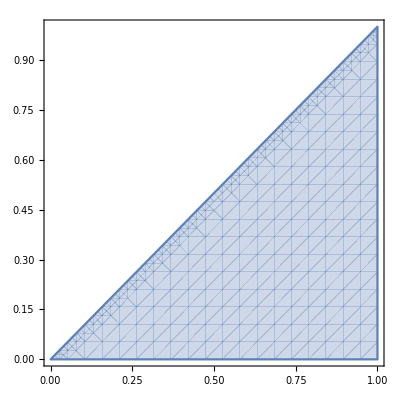

```mathematica
RegionPlot[ 0<x<1 && 0<y<x,{x,0,1},{y,0,1}]
```

```mathematica
Integrate[Integrate[1, {y, 0, Log[x]} ],{x, 1, 2}]
```

-1+Log[4]

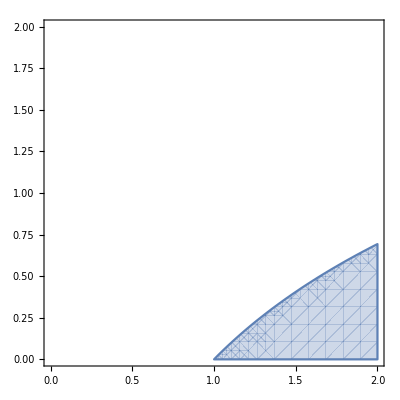

```mathematica
RegionPlot[ 1<x<2 && 0<y<Log[x],{x,0,2},{y,0,2}]
```

Exercise 11

```mathematica
Integrate[Integrate[1, {x, y, 2-y} ],{y, 0, 1}]
```

1

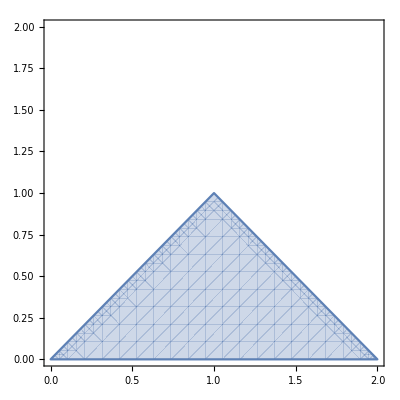

```mathematica
RegionPlot[ 0<y<1&&y<x<(2-y),{x,0,2},{y,0,2}]
```

```mathematica
Integrate[Integrate[1, {x, y,Exp[y]} ],{y, 0, 1}]
```

-3/2+ⅇ

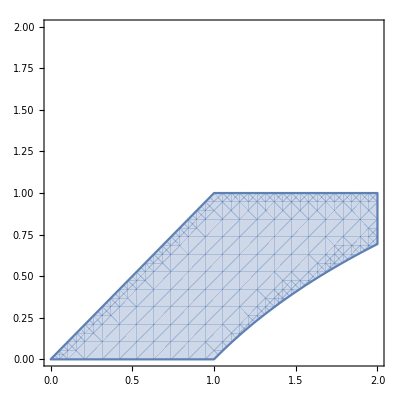

```mathematica
RegionPlot[ 0<y<1&&y<x<Exp[y],{x,0,2},{y,0,2}]
```

Exercise 12

```mathematica
Integrate[Integrate[1, {x, y,1} ],{y, 0, 1}]
```

1/2

```mathematica
RegionPlot[ 0<y<1&&y<x<1,{x,0,1},{y,0,1}]
```

-Graphics-

```mathematica
Integrate[Integrate[1, {x, Exp[y],2} ],{y, 0, Log[2]}]
```

-1+Log[4]

```mathematica
RegionPlot[ 0<y<Log[2]&&Exp[y]<x<2,{x,0,2},{y,0,2}]
```

-Graphics-

```mathematica
Integrate[Integrate[x, {y, 0, 1} ],{x, 0, 1}]+Integrate[Integrate[-x, {y, 1, 2} ],{x, 1, 2}]
```

-1

```mathematica
RegionPlot[ 0<y<1&&y<x<(2-y),{x,0,2},{y,0,2}]
```

-Graphics-

```mathematica
Integrate[Integrate[x, {y, 0, 1} ],{x, 0, 1}]+Integrate[Integrate[1, {y, Log[x], 2} ],{x, 1, 2}]
```

7/2-Log[4]

```mathematica
RegionPlot[ 0<y<1&&y<x<Exp[y],{x,0,2},{y,0,2}]
```

-Graphics-

Exercise 13

```mathematica
Integrate[Integrate[(4y)/((x^3)+3), {y, 0, 2x} ],{x, 1, 2}]
```

8/3 Log[11/4]

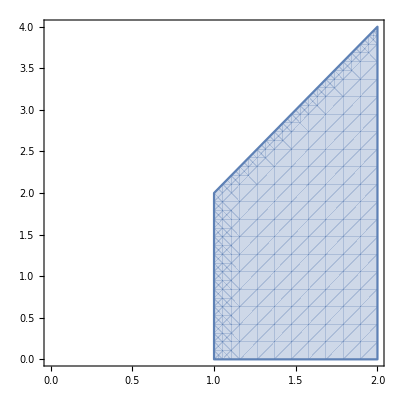

```mathematica
RegionPlot[ 1<x<2 && 0<y<2*x,{x,0,2},{y,0,4}]
```

```mathematica
Integrate[Integrate[x*Cos[y], {y, 0, x^2} ],{x, 0, 1}]
```

Sin[1/2]^2

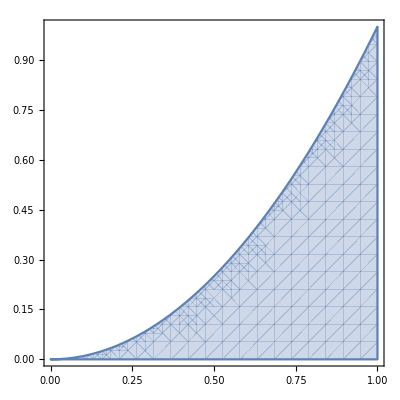

```mathematica
RegionPlot[ 0<x<1 && 0<y<x^2,{x,0,1},{y,0,1}]
```

Exercise 14

```mathematica
Integrate[Integrate[2.7, {x, 0, Sqrt[y]} ],{y, 0, 10}]
```

56.921

```mathematica
Integrate[Integrate[x*2.7, {x, 0, Sqrt[y]} ],{y, 0, 10}]/56.9
```

1.18629

```mathematica
Integrate[Integrate[y*2.7, {x, 0, Sqrt[y]} ],{y, 0, 10}]/56.9
```

6.00221

# 2. Multiple Integrals

The main functions used in this section are the derivative D, the integral Integrate, and the function RegionPlot to visualize regions. To learn more about these functions you can either open up the Mathematica documentation in a new window, or you can get the basic syntax using a question mark before the function name and using shift+return.

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
?RegionPlot
```

RegionPlot[pred,{x,x_min,x_max},{y,y_min,y_max}] makes a plot showing the region in which pred is True.

Here are some basic examples to get you started:

The derivative of x^n

```mathematica
D[x^n,x]
```

n x^(-1+n)

The anti-derivative or indefinite integral of x^n

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

The definite integral of x^nfrom x = 1 to x = 2.

```mathematica
Integrate[x^n,{x,1,2}]
```

(-1+2^(1+n))/(1+n)

The region in the plane bounded by y = x, x = 0, y = 2.

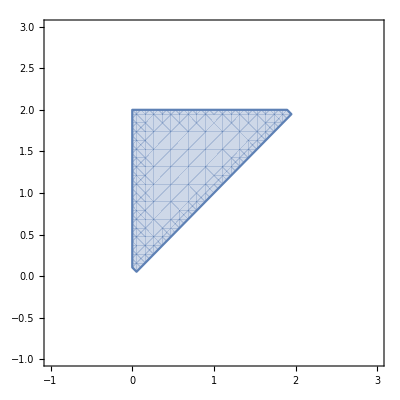

```mathematica
RegionPlot[y> x&&y<2&&x>0,{x,-1,3},{y,-1,3}]
```

The area of this region. Notice that the order of integration here really matters.

```mathematica
area = Integrate[1,{x,0,2},{y,x,2}]
```

2

The center of mass of this region, also known as the centroid for a geometrical shape.

```mathematica
xcom = Integrate[x,{x,0,2},{y,x,2}]/Integrate[1,{x,0,2},{y,x,2}]
ycom = Integrate[y,{x,0,2},{y,x,2}]/Integrate[1,{x,0,2},{y,x,2}]
```

2/3

4/3

Now we plot the plate and the center of mass of the plate and check that it makes sense.

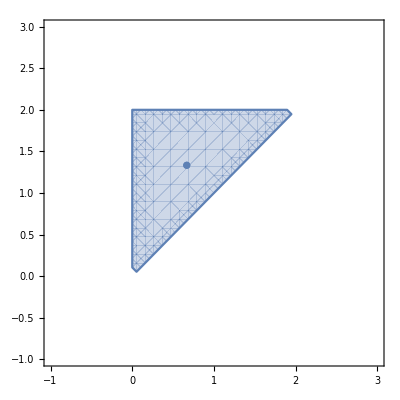

```mathematica
Show[RegionPlot[y> x&&y<2&&x>0,{x,-1,3},{y,-1,3}],ListPlot[{{xcom,ycom}}]]
```

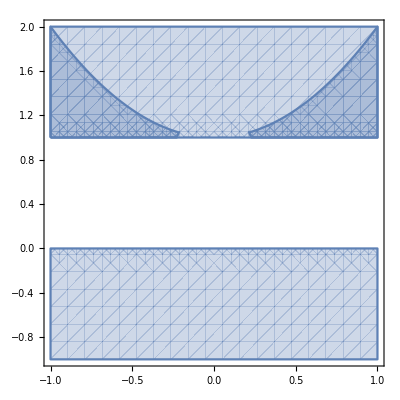

```mathematica
Show[RegionPlot[ -1<x<1 && -1<y<y^2,{x,-1,1},{y,-1,2}] ,RegionPlot[1<y<1+x^2&&-1<x<1 ,{x,-1,1},{y,-1,2} ] ]
```

```mathematica
?ImplicitRegion
```

ImplicitRegion[cond,{x_1,…,x_n}] represents a region in ℝ^n that satisfies the conditions cond. 
ImplicitRegion[cond,{{x_1,a_1,b_1},…}] represents a region in ℝ^n that satisfies the conditions cond as well as a_1≤x_1≤b_1 etc.

```mathematica
R=ImplicitRegion[-1<y<1 && -1<x<y^2,{{x,-1,1},{y,-1,2}}]
```

ImplicitRegion[-1<y<1&&-1<x<y^2&&-1≤x≤1&&-1≤y≤2,{x,y}]

```mathematica
T=ImplicitRegion[1<y<1+x^2 && -1<x<1,{{x,-1,1},{y,-1,2}}]
```

ImplicitRegion[1<y<1+x^2&&-1<x<1&&-1≤x≤1&&-1≤y≤2,{x,y}]

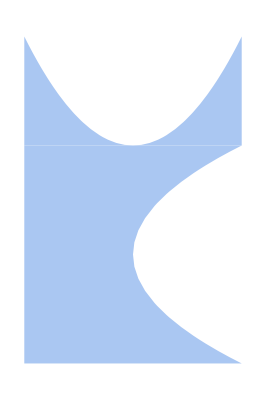

```mathematica
Show[Region[R], Region[T]]
```